```mathematica
ClearAll["Global`*"]  (*2-step 2-stage 7-order ThDTSRK27  A-stable*)
Remove["Global`*"]
ClearAll["p*"]
ClearAll["A*"]
ClearAll["v*"]
ClearAll["w*"]
ClearAll["z*"]
ClearAll["a21*"]
θ=0;  (*a21=0.5;*)
tht=θ;
vvv1=(-209+300 a21-6270 a21^2+15540 a21^3+tht+20 a21 tht+30 a21^2 tht+140 a21^3 tht)/(1680 (a21+10 a21^3));
vvv2=(209-tht)/(1680 (a21+10 a21^3));
vv1=(-45+627 a21-868 a21^2-3 tht-3 a21 tht-28 a21^2 tht)/(28 (1+10 a21^2));  vv2=0;
v1=(105-627 a21+1050 a21^2+7 tht+3 a21 tht+70 a21^2 tht)/(14 (1+10 a21^2));   v2=0;
w1=(-91+627 a21-910 a21^2+7 tht-3 a21 tht+70 a21^2 tht)/(14 (1+10 a21^2));    w2=0;
ww1=(-123+627 a21-812 a21^2+3 tht-3 a21 tht+28 a21^2 tht)/(28 (1+10 a21^2));   ww2=0;
www1=(209-1940 a21+6270 a21^2-6860 a21^3-tht+20 a21 tht-30 a21^2 tht+140 a21^3 tht)/(1680 (a21+10 a21^3));
www2=(-209+tht)/(1680 (a21+10 a21^3));

nn=2;
e=Table[1,{ii,nn},{i,1}];
v=({{v1, v2}});   v̂=({{vv1, vv2}}); v̄=({{vvv1, vvv2}});
w=({{w1, w2}});   ŵ=({{ww1, ww2}}); w̄=({{www1, www2}});
A=({{0, 0}, {a21, 0}}); Â=({{0, 0}, {a21^2/2, 0}});Ā=({{0, 0}, {a21^3/6, 0}});

S=Table[0,{ii,nn+nn},{i,nn+nn}];A1=B1=C1=S;
SS=Table[0,{ii,nn+2},{i,nn+nn}];A2=B2=C2=SS;
D1=D2=Table[0,{ii,nn+nn},{i,nn+2}];
e44=IdentityMatrix[nn+nn];  e21=Table[1,{ii,nn},{i,1}];
 
A1[[1;;nn]][[1;;nn]]=A; A1[[nn+1;;2*nn]][[nn+1;;2*nn]]=A; A1//MatrixForm;
B1[[1;;nn]][[1;;nn]]=Â; B1[[nn+1;;2*nn]][[nn+1;;2*nn]]=Â; B1//MatrixForm;
C1[[1;;nn]][[1;;nn]]=Ā; C1[[nn+1;;2*nn]][[nn+1;;2*nn]]=Ā; C1//MatrixForm;
D1[[1;;nn]][[nn+1;;nn+1]]=e21;D1[[nn+1;;2*nn]][[nn+2;;nn+2]]=e21;D1//MatrixForm;


A2[[1;;nn]][[nn+1;;2*nn]]=A; A2[[2+nn;;2+nn]][[1;;nn]]=w;
A2[[2+nn;;2+nn]][[nn+1;;2*nn]]=v; A2//MatrixForm;
B2[[1;;nn]][[nn+1;;2*nn]]=Â; B2[[2+nn;;2+nn]][[1;;nn]]=ŵ;
B2[[2+nn;;2+nn]][[nn+1;;2*nn]]=v̂; B2//MatrixForm;
C2[[1;;nn]][[nn+1;;2*nn]]=Ā; C2[[2+nn;;2+nn]][[1;;nn]]=w̄;
C2[[2+nn;;2+nn]][[nn+1;;2*nn]]=v̄; C2//MatrixForm;
D2[[1;;nn]][[nn+2;;nn+2]]=e21;D2[[nn+1]][[nn+2]]=1;
D2[[nn+2]][[nn+1]]=θ; D2[[nn+2]][[nn+2]]=1-θ; D2//MatrixForm;
f[z_]:=Det[ξ*e44-D2 -(z*A2+z^2*B2+z^3*C2).Inverse[e44-z*A1-z^2*B1-z^3*C1] .D1 ] //Expand;
f[z]//FullSimplify//Rationalize
  ff=(-1254 z^4 (-1+ξ)-627 a21 z^5 (-1+ξ)-209 a21^2 z^6 (-1+ξ)+10080 (1+10 a21^2) (-1+ξ) ξ-720 z (-91-627 a21 (-1+ξ)+105 ξ+70 a21^2 (-13+15 ξ))+360 z^2 (123+45 ξ-627 a21 (1+ξ)+28 a21^2 (29+31 ξ))-60 z^3 (-194-627 a21 (-1+ξ)+30 ξ+14 a21^2 (-49+111 ξ)));
sol=Solve[ff==0,{ ξ}]//FullSimplify//Rationalize
(*FindMinimum[{z,Abs[gg[z]]==1&&0.1<a21<1&&-8<z<-0.1},{z,a21}]*)
```

ClearAll::wrsym: Symbol AASTriangle is Protected.

ClearAll::wrsym: Symbol AbelianGroup is Protected.

ClearAll::wrsym: Symbol Abort is Protected.

General::stop: Further output of ClearAll::wrsym will be suppressed during this calculation.

1/(10080 (1+10 a21^2))ξ^2 (-1254 z^4 (-1+ξ)-627 a21 z^5 (-1+ξ)-209 a21^2 z^6 (-1+ξ)+10080 (1+10 a21^2) (-1+ξ) ξ-720 z (-91-627 a21 (-1+ξ)+105 ξ+70 a21^2 (-13+15 ξ))+360 z^2 (123+45 ξ-627 a21 (1+ξ)+28 a21^2 (29+31 ξ))-60 z^3 (-194-627 a21 (-1+ξ)+30 ξ+14 a21^2 (-49+111 ξ)))

{{ξ→1/(20160 (1+10 a21^2))(627 a21 z (-720+z (360-60 z+z^3))+a21^2 (100800+z (756000+z (-312480+93240 z+209 z^4)))+6 (1680+z (12600+z (-2700+z (300+209 z))))-√(-40320 (1+10 a21^2) z (65520+6 z (7380+z (1940+209 z))+627 a21 (-720+z (-360-60 z+z^3))+a21^2 (655200+z (292320+41160 z+209 z^4)))+(5040 (2+15 z)+6 z^2 (-2700+z (300+209 z))+627 a21 z (-720+z (360-60 z+z^3))+a21^2 (100800+z (756000+z (-312480+93240 z+209 z^4))))^2))},{ξ→1/(20160 (1+10 a21^2))(627 a21 z (-720+z (360-60 z+z^3))+a21^2 (100800+z (756000+z (-312480+93240 z+209 z^4)))+6 (1680+z (12600+z (-2700+z (300+209 z))))+√(-40320 (1+10 a21^2) z (65520+6 z (7380+z (1940+209 z))+627 a21 (-720+z (-360-60 z+z^3))+a21^2 (655200+z (292320+41160 z+209 z^4)))+(5040 (2+15 z)+6 z^2 (-2700+z (300+209 z))+627 a21 z (-720+z (360-60 z+z^3))+a21^2 (100800+z (756000+z (-312480+93240 z+209 z^4))))^2))}}

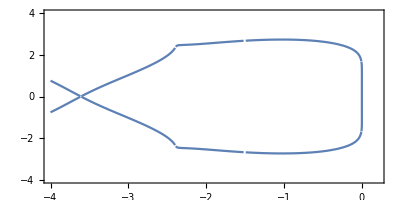

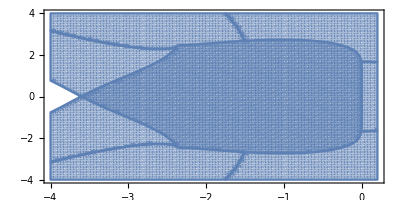

```mathematica
ClearAll["Global`*"]   (*2-step 2-stage 7-order ThDTSRK27  A-stable *)
Remove["Global`*"]
ClearAll["x*"]
ClearAll["y*"]
ClearAll["z*"]
ClearAll["f*"]
θ=0.0;     a21=0.5;
z=x+I*y;
f[z_]:=1/(20160 (1+10 a21^2))(627 a21 z (-720+z (360-60 z+z^3))+a21^2 (100800+z (756000+z (-312480+93240 z+209 z^4)))+6 (1680+z (12600+z (-2700+z (300+209 z))))-√(-40320 (1+10 a21^2) z (65520+6 z (7380+z (1940+209 z))+627 a21 (-720+z (-360-60 z+z^3))+a21^2 (655200+z (292320+41160 z+209 z^4)))+(5040 (2+15 z)+6 z^2 (-2700+z (300+209 z))+627 a21 z (-720+z (360-60 z+z^3))+a21^2 (100800+z (756000+z (-312480+93240 z+209 z^4))))^2));
ss1=ContourPlot[Abs[f[z]]==1,{x,-4,0.2},{y,-4.,4.},AspectRatio->1.2,PlotPoints->50] ;
rr1=RegionPlot[Abs[f[z]]<=1,{x,-4,0.2},{y,-4.,4.},AspectRatio->1.2,PlotPoints->100]  ;
f[z_]:=1/(20160 (1+10 a21^2))(627 a21 z (-720+z (360-60 z+z^3))+a21^2 (100800+z (756000+z (-312480+93240 z+209 z^4)))+6 (1680+z (12600+z (-2700+z (300+209 z))))+√(-40320 (1+10 a21^2) z (65520+6 z (7380+z (1940+209 z))+627 a21 (-720+z (-360-60 z+z^3))+a21^2 (655200+z (292320+41160 z+209 z^4)))+(5040 (2+15 z)+6 z^2 (-2700+z (300+209 z))+627 a21 z (-720+z (360-60 z+z^3))+a21^2 (100800+z (756000+z (-312480+93240 z+209 z^4))))^2));
ss2=ContourPlot[Abs[f[z]]==1,{x,-4,0.2},{y,-4.,4.},AspectRatio->1.2,PlotPoints->50] ;
rr2=RegionPlot[Abs[f[z]]<=1,{x,-4,0.2},{y,-4.,4.},AspectRatio->1.2,PlotPoints->100]  ;
Show[ss1,ss2,AspectRatio->0.5]
Show[rr1,rr2,AspectRatio->0.5]
```

```mathematica
ClearAll["Global`*"]  (*2-step 2-stage 6-order ThDTSRK26  A-stable*)
Remove["Global`*"]
ClearAll["p*"]
ClearAll["A*"]
ClearAll["v*"]
ClearAll["w*"]
ClearAll["z*"]
ClearAll["a21*"]

θ=0;    tht=θ;
vvv1=1/120 (111-120 vvv2-1080 a21 vvv2-2160 a21^2 vvv2-1200 a21^3 vvv2+120 a21 ww2+360 a21^2 ww2+1200 a21^3 ww2-360 a21 www2+1440 a21^2 www2-1200 a21^3 www2+θ);vv1=1/10 (-31+360 a21 vvv2+960 a21^2 vvv2+600 a21^3 vvv2+10 ww2-60 a21^2 ww2-600 a21^3 ww2+240 a21 www2-840 a21^2 www2+600 a21^3 www2-θ);
vv2=-ww2;
v1=1/2 (15-120 a21 vvv2-360 a21^2 vvv2-240 a21^3 vvv2+240 a21^3 ww2-120 a21 www2+360 a21^2 www2-240 a21^3 www2+θ);
v2=0;
w1=1/2 (-13+120 a21 vvv2+360 a21^2 vvv2+240 a21^3 vvv2-240 a21^3 ww2+120 a21 www2-360 a21^2 www2+240 a21^3 www2+θ);
w2=0;
ww1=1/10 (-29+240 a21 vvv2+840 a21^2 vvv2+600 a21^3 vvv2-10 ww2+60 a21^2 ww2-600 a21^3 ww2+360 a21 www2-960 a21^2 www2+600 a21^3 www2+θ);www1=1/120 (-49+360 a21 vvv2+1440 a21^2 vvv2+1200 a21^3 vvv2-120 a21 ww2+360 a21^2 ww2-1200 a21^3 ww2-120 www2+1080 a21 www2-2160 a21^2 www2+1200 a21^3 www2+θ); 
nn=2;    e=Table[1,{ii,nn},{i,1}];
v=({{v1, v2}});   v̂=({{vv1, vv2}}); v̄=({{vvv1, vvv2}});
w=({{w1, w2}});   ŵ=({{ww1, ww2}}); w̄=({{www1, www2}});
A=({{0, 0}, {a21, 0}}); Â=({{0, 0}, {a21^2/2, 0}});Ā=({{0, 0}, {a21^3/6, 0}});

S=Table[0,{ii,nn+nn},{i,nn+nn}];A1=B1=C1=S;
SS=Table[0,{ii,nn+2},{i,nn+nn}];A2=B2=C2=SS;
D1=D2=Table[0,{ii,nn+nn},{i,nn+2}];
e44=IdentityMatrix[nn+nn];  e21=Table[1,{ii,nn},{i,1}];
 
A1[[1;;nn]][[1;;nn]]=A; A1[[nn+1;;2*nn]][[nn+1;;2*nn]]=A; A1//MatrixForm;
B1[[1;;nn]][[1;;nn]]=Â; B1[[nn+1;;2*nn]][[nn+1;;2*nn]]=Â; B1//MatrixForm;
C1[[1;;nn]][[1;;nn]]=Ā; C1[[nn+1;;2*nn]][[nn+1;;2*nn]]=Ā; C1//MatrixForm;
D1[[1;;nn]][[nn+1;;nn+1]]=e21;D1[[nn+1;;2*nn]][[nn+2;;nn+2]]=e21;D1//MatrixForm;

A2[[1;;nn]][[nn+1;;2*nn]]=A; A2[[2+nn;;2+nn]][[1;;nn]]=w;
A2[[2+nn;;2+nn]][[nn+1;;2*nn]]=v; A2//MatrixForm;
B2[[1;;nn]][[nn+1;;2*nn]]=Â; B2[[2+nn;;2+nn]][[1;;nn]]=ŵ;
B2[[2+nn;;2+nn]][[nn+1;;2*nn]]=v̂; B2//MatrixForm;
C2[[1;;nn]][[nn+1;;2*nn]]=Ā; C2[[2+nn;;2+nn]][[1;;nn]]=w̄;
C2[[2+nn;;2+nn]][[nn+1;;2*nn]]=v̄; C2//MatrixForm;
D2[[1;;nn]][[nn+2;;nn+2]]=e21;D2[[nn+1]][[nn+2]]=1;
D2[[nn+2]][[nn+1]]=θ; D2[[nn+2]][[nn+2]]=1-θ; D2//MatrixForm;
f[z_]:=Det[ξ*e44-D2 -(z*A2+z^2*B2+z^3*C2).Inverse[e44-z*A1-z^2*B1-z^3*C1] .D1 ] //Expand;
ff=(60 z (13+120 a21 ((1+a21) (1+2 a21) vvv2+www2-3 a21 www2+2 a21^2 (-ww2+www2)) (-1+ξ)-15 ξ)+120 (-1+ξ) ξ-20 a21^3 z^6 (www2+vvv2 ξ)+20 a21^2 z^5 (a21 ww2 (-1+ξ)-3 (www2+vvv2 ξ))+60 a21 z^4 (a21 ww2 (-1+ξ)-2 (www2+vvv2 ξ))+z^3 (49+1200 a21^3 (vvv2-ww2+www2) (-1+ξ)-111 ξ-360 a21^2 (4 vvv2+ww2-6 www2+(-6 vvv2+ww2+4 www2) ξ)+360 a21 (www2 (-3+ξ)+vvv2 (-1+3 ξ)))-12 z^2 (-29-31 ξ+60 a21 (6 www2+4 www2 ξ-10 a21^2 (ww2-www2) (1+ξ)+2 (1+a21) vvv2 (2+3 ξ+5 a21 (1+ξ))+a21 (ww2-ww2 ξ-2 www2 (8+7 ξ)))));

f[z]//FullSimplify
sol=Solve[ff==0,{ ξ}]//Expand

(*FindMinimum[{z,Abs[f[z]]==0&&-1<ξ<1&&z<0},{z,ξ}]*)
```

ClearAll::wrsym: Symbol AASTriangle is Protected.

ClearAll::wrsym: Symbol AbelianGroup is Protected.

ClearAll::wrsym: Symbol Abort is Protected.

General::stop: Further output of ClearAll::wrsym will be suppressed during this calculation.

1/120 ξ^2 (60 z (13+120 a21 ((1+a21) (1+2 a21) vvv2+www2-3 a21 www2+2 a21^2 (-ww2+www2)) (-1+ξ)-15 ξ)+120 (-1+ξ) ξ-20 a21^3 z^6 (www2+vvv2 ξ)+20 a21^2 z^5 (a21 ww2 (-1+ξ)-3 (www2+vvv2 ξ))+60 a21 z^4 (a21 ww2 (-1+ξ)-2 (www2+vvv2 ξ))+z^3 (49+1200 a21^3 (vvv2-ww2+www2) (-1+ξ)-111 ξ-360 a21^2 (4 vvv2+ww2-6 www2+(-6 vvv2+ww2+4 www2) ξ)+360 a21 (www2 (-3+ξ)+vvv2 (-1+3 ξ)))-12 z^2 (-29-31 ξ+60 a21 (6 www2+4 www2 ξ-10 a21^2 (ww2-www2) (1+ξ)+2 (1+a21) vvv2 (2+3 ξ+5 a21 (1+ξ))+a21 (ww2-ww2 ξ-2 www2 (8+7 ξ)))))

{{ξ→1/2+(15 z)/4-30 a21 vvv2 z-90 a21^2 vvv2 z-60 a21^3 vvv2 z+60 a21^3 ww2 z-30 a21 www2 z+90 a21^2 www2 z-60 a21^3 www2 z-(31 z^2)/20+18 a21 vvv2 z^2+48 a21^2 vvv2 z^2+30 a21^3 vvv2 z^2-3 a21^2 ww2 z^2-30 a21^3 ww2 z^2+12 a21 www2 z^2-42 a21^2 www2 z^2+30 a21^3 www2 z^2+(37 z^3)/80-9/2 a21 vvv2 z^3-9 a21^2 vvv2 z^3-5 a21^3 vvv2 z^3+3/2 a21^2 ww2 z^3+5 a21^3 ww2 z^3-3/2 a21 www2 z^3+6 a21^2 www2 z^3-5 a21^3 www2 z^3+1/2 a21 vvv2 z^4-1/4 a21^2 ww2 z^4+1/4 a21^2 vvv2 z^5-1/12 a21^3 ww2 z^5+1/12 a21^3 vvv2 z^6-1/240 √((-120-900 z+7200 a21 vvv2 z+21600 a21^2 vvv2 z+14400 a21^3 vvv2 z-14400 a21^3 ww2 z+7200 a21 www2 z-21600 a21^2 www2 z+14400 a21^3 www2 z+372 z^2-4320 a21 vvv2 z^2-11520 a21^2 vvv2 z^2-7200 a21^3 vvv2 z^2+720 a21^2 ww2 z^2+7200 a21^3 ww2 z^2-2880 a21 www2 z^2+10080 a21^2 www2 z^2-7200 a21^3 www2 z^2-111 z^3+1080 a21 vvv2 z^3+2160 a21^2 vvv2 z^3+1200 a21^3 vvv2 z^3-360 a21^2 ww2 z^3-1200 a21^3 ww2 z^3+360 a21 www2 z^3-1440 a21^2 www2 z^3+1200 a21^3 www2 z^3-120 a21 vvv2 z^4+60 a21^2 ww2 z^4-60 a21^2 vvv2 z^5+20 a21^3 ww2 z^5-20 a21^3 vvv2 z^6)^2-480 (780 z-7200 a21 vvv2 z-21600 a21^2 vvv2 z-14400 a21^3 vvv2 z+14400 a21^3 ww2 z-7200 a21 www2 z+21600 a21^2 www2 z-14400 a21^3 www2 z+348 z^2-2880 a21 vvv2 z^2-10080 a21^2 vvv2 z^2-7200 a21^3 vvv2 z^2-720 a21^2 ww2 z^2+7200 a21^3 ww2 z^2-4320 a21 www2 z^2+11520 a21^2 www2 z^2-7200 a21^3 www2 z^2+49 z^3-360 a21 vvv2 z^3-1440 a21^2 vvv2 z^3-1200 a21^3 vvv2 z^3-360 a21^2 ww2 z^3+1200 a21^3 ww2 z^3-1080 a21 www2 z^3+2160 a21^2 www2 z^3-1200 a21^3 www2 z^3-60 a21^2 ww2 z^4-120 a21 www2 z^4-20 a21^3 ww2 z^5-60 a21^2 www2 z^5-20 a21^3 www2 z^6))},{ξ→1/2+(15 z)/4-30 a21 vvv2 z-90 a21^2 vvv2 z-60 a21^3 vvv2 z+60 a21^3 ww2 z-30 a21 www2 z+90 a21^2 www2 z-60 a21^3 www2 z-(31 z^2)/20+18 a21 vvv2 z^2+48 a21^2 vvv2 z^2+30 a21^3 vvv2 z^2-3 a21^2 ww2 z^2-30 a21^3 ww2 z^2+12 a21 www2 z^2-42 a21^2 www2 z^2+30 a21^3 www2 z^2+(37 z^3)/80-9/2 a21 vvv2 z^3-9 a21^2 vvv2 z^3-5 a21^3 vvv2 z^3+3/2 a21^2 ww2 z^3+5 a21^3 ww2 z^3-3/2 a21 www2 z^3+6 a21^2 www2 z^3-5 a21^3 www2 z^3+1/2 a21 vvv2 z^4-1/4 a21^2 ww2 z^4+1/4 a21^2 vvv2 z^5-1/12 a21^3 ww2 z^5+1/12 a21^3 vvv2 z^6+1/240 √((-120-900 z+7200 a21 vvv2 z+21600 a21^2 vvv2 z+14400 a21^3 vvv2 z-14400 a21^3 ww2 z+7200 a21 www2 z-21600 a21^2 www2 z+14400 a21^3 www2 z+372 z^2-4320 a21 vvv2 z^2-11520 a21^2 vvv2 z^2-7200 a21^3 vvv2 z^2+720 a21^2 ww2 z^2+7200 a21^3 ww2 z^2-2880 a21 www2 z^2+10080 a21^2 www2 z^2-7200 a21^3 www2 z^2-111 z^3+1080 a21 vvv2 z^3+2160 a21^2 vvv2 z^3+1200 a21^3 vvv2 z^3-360 a21^2 ww2 z^3-1200 a21^3 ww2 z^3+360 a21 www2 z^3-1440 a21^2 www2 z^3+1200 a21^3 www2 z^3-120 a21 vvv2 z^4+60 a21^2 ww2 z^4-60 a21^2 vvv2 z^5+20 a21^3 ww2 z^5-20 a21^3 vvv2 z^6)^2-480 (780 z-7200 a21 vvv2 z-21600 a21^2 vvv2 z-14400 a21^3 vvv2 z+14400 a21^3 ww2 z-7200 a21 www2 z+21600 a21^2 www2 z-14400 a21^3 www2 z+348 z^2-2880 a21 vvv2 z^2-10080 a21^2 vvv2 z^2-7200 a21^3 vvv2 z^2-720 a21^2 ww2 z^2+7200 a21^3 ww2 z^2-4320 a21 www2 z^2+11520 a21^2 www2 z^2-7200 a21^3 www2 z^2+49 z^3-360 a21 vvv2 z^3-1440 a21^2 vvv2 z^3-1200 a21^3 vvv2 z^3-360 a21^2 ww2 z^3+1200 a21^3 ww2 z^3-1080 a21 www2 z^3+2160 a21^2 www2 z^3-1200 a21^3 www2 z^3-60 a21^2 ww2 z^4-120 a21 www2 z^4-20 a21^3 ww2 z^5-60 a21^2 www2 z^5-20 a21^3 www2 z^6))}}

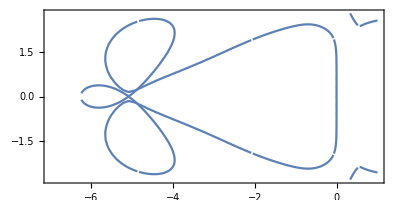

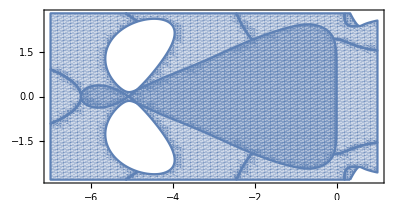

```mathematica
ClearAll["Global`*"]   (*2-step 2-stage 6-order ThDTSRK26  A-stable *)
Remove["Global`*"]
ClearAll["x*"]
ClearAll["y*"]
ClearAll["z*"]
ClearAll["f*"]
θ=0;
a21=0.587325896573798; ww2=-0.141169152307059; vvv2=0.0243580486114999; www2=-0.0227607642077618;
(*0.587325896573798-0.141169152307059 0.0243580486114999-0.0227607642077618-6.26637023361276*)
z=x+I*y;
f[z_]:=1/2+(15 z)/4-30 a21 vvv2 z-90 a21^2 vvv2 z-60 a21^3 vvv2 z+60 a21^3 ww2 z-30 a21 www2 z+90 a21^2 www2 z-60 a21^3 www2 z-(31 z^2)/20+18 a21 vvv2 z^2+48 a21^2 vvv2 z^2+30 a21^3 vvv2 z^2-3 a21^2 ww2 z^2-30 a21^3 ww2 z^2+12 a21 www2 z^2-42 a21^2 www2 z^2+30 a21^3 www2 z^2+(37 z^3)/80-9/2 a21 vvv2 z^3-9 a21^2 vvv2 z^3-5 a21^3 vvv2 z^3+3/2 a21^2 ww2 z^3+5 a21^3 ww2 z^3-3/2 a21 www2 z^3+6 a21^2 www2 z^3-5 a21^3 www2 z^3+1/2 a21 vvv2 z^4-1/4 a21^2 ww2 z^4+1/4 a21^2 vvv2 z^5-1/12 a21^3 ww2 z^5+1/12 a21^3 vvv2 z^6-1/240 √((-120-900 z+7200 a21 vvv2 z+21600 a21^2 vvv2 z+14400 a21^3 vvv2 z-14400 a21^3 ww2 z+7200 a21 www2 z-21600 a21^2 www2 z+14400 a21^3 www2 z+372 z^2-4320 a21 vvv2 z^2-11520 a21^2 vvv2 z^2-7200 a21^3 vvv2 z^2+720 a21^2 ww2 z^2+7200 a21^3 ww2 z^2-2880 a21 www2 z^2+10080 a21^2 www2 z^2-7200 a21^3 www2 z^2-111 z^3+1080 a21 vvv2 z^3+2160 a21^2 vvv2 z^3+1200 a21^3 vvv2 z^3-360 a21^2 ww2 z^3-1200 a21^3 ww2 z^3+360 a21 www2 z^3-1440 a21^2 www2 z^3+1200 a21^3 www2 z^3-120 a21 vvv2 z^4+60 a21^2 ww2 z^4-60 a21^2 vvv2 z^5+20 a21^3 ww2 z^5-20 a21^3 vvv2 z^6)^2-480 (780 z-7200 a21 vvv2 z-21600 a21^2 vvv2 z-14400 a21^3 vvv2 z+14400 a21^3 ww2 z-7200 a21 www2 z+21600 a21^2 www2 z-14400 a21^3 www2 z+348 z^2-2880 a21 vvv2 z^2-10080 a21^2 vvv2 z^2-7200 a21^3 vvv2 z^2-720 a21^2 ww2 z^2+7200 a21^3 ww2 z^2-4320 a21 www2 z^2+11520 a21^2 www2 z^2-7200 a21^3 www2 z^2+49 z^3-360 a21 vvv2 z^3-1440 a21^2 vvv2 z^3-1200 a21^3 vvv2 z^3-360 a21^2 ww2 z^3+1200 a21^3 ww2 z^3-1080 a21 www2 z^3+2160 a21^2 www2 z^3-1200 a21^3 www2 z^3-60 a21^2 ww2 z^4-120 a21 www2 z^4-20 a21^3 ww2 z^5-60 a21^2 www2 z^5-20 a21^3 www2 z^6));
ss1=ContourPlot[Abs[f[z]]==1,{x,-7,1},{y,-2.8,2.8},AspectRatio->1.2,PlotPoints->20] ;
rr1=RegionPlot[Abs[f[z]]<=1,{x,-7,1},{y,-2.8,2.8},AspectRatio->1.2,PlotPoints->50]  ;
f[z_]:= 1/2+(15 z)/4-30 a21 vvv2 z-90 a21^2 vvv2 z-60 a21^3 vvv2 z+60 a21^3 ww2 z-30 a21 www2 z+90 a21^2 www2 z-60 a21^3 www2 z-(31 z^2)/20+18 a21 vvv2 z^2+48 a21^2 vvv2 z^2+30 a21^3 vvv2 z^2-3 a21^2 ww2 z^2-30 a21^3 ww2 z^2+12 a21 www2 z^2-42 a21^2 www2 z^2+30 a21^3 www2 z^2+(37 z^3)/80-9/2 a21 vvv2 z^3-9 a21^2 vvv2 z^3-5 a21^3 vvv2 z^3+3/2 a21^2 ww2 z^3+5 a21^3 ww2 z^3-3/2 a21 www2 z^3+6 a21^2 www2 z^3-5 a21^3 www2 z^3+1/2 a21 vvv2 z^4-1/4 a21^2 ww2 z^4+1/4 a21^2 vvv2 z^5-1/12 a21^3 ww2 z^5+1/12 a21^3 vvv2 z^6+1/240 √((-120-900 z+7200 a21 vvv2 z+21600 a21^2 vvv2 z+14400 a21^3 vvv2 z-14400 a21^3 ww2 z+7200 a21 www2 z-21600 a21^2 www2 z+14400 a21^3 www2 z+372 z^2-4320 a21 vvv2 z^2-11520 a21^2 vvv2 z^2-7200 a21^3 vvv2 z^2+720 a21^2 ww2 z^2+7200 a21^3 ww2 z^2-2880 a21 www2 z^2+10080 a21^2 www2 z^2-7200 a21^3 www2 z^2-111 z^3+1080 a21 vvv2 z^3+2160 a21^2 vvv2 z^3+1200 a21^3 vvv2 z^3-360 a21^2 ww2 z^3-1200 a21^3 ww2 z^3+360 a21 www2 z^3-1440 a21^2 www2 z^3+1200 a21^3 www2 z^3-120 a21 vvv2 z^4+60 a21^2 ww2 z^4-60 a21^2 vvv2 z^5+20 a21^3 ww2 z^5-20 a21^3 vvv2 z^6)^2-480 (780 z-7200 a21 vvv2 z-21600 a21^2 vvv2 z-14400 a21^3 vvv2 z+14400 a21^3 ww2 z-7200 a21 www2 z+21600 a21^2 www2 z-14400 a21^3 www2 z+348 z^2-2880 a21 vvv2 z^2-10080 a21^2 vvv2 z^2-7200 a21^3 vvv2 z^2-720 a21^2 ww2 z^2+7200 a21^3 ww2 z^2-4320 a21 www2 z^2+11520 a21^2 www2 z^2-7200 a21^3 www2 z^2+49 z^3-360 a21 vvv2 z^3-1440 a21^2 vvv2 z^3-1200 a21^3 vvv2 z^3-360 a21^2 ww2 z^3+1200 a21^3 ww2 z^3-1080 a21 www2 z^3+2160 a21^2 www2 z^3-1200 a21^3 www2 z^3-60 a21^2 ww2 z^4-120 a21 www2 z^4-20 a21^3 ww2 z^5-60 a21^2 www2 z^5-20 a21^3 www2 z^6));
ss2=ContourPlot[Abs[f[z]]==1,{x,-7,1},{y,-2.8,2.8},AspectRatio->1.2,PlotPoints->20] ;
rr2=RegionPlot[Abs[f[z]]<=1,{x,-7,1},{y,-2.8,2.8},AspectRatio->1.2,PlotPoints->50]  ;
Show[ss1,ss2,AspectRatio->0.5]
Show[rr1,rr2,AspectRatio->0.5]
```

```mathematica
ClearAll["Global`*"]  (*2-step 2-stage 5-order ThDTSRK25  A-stable*)
Remove["Global`*"]
ClearAll["p*"]
ClearAll["A*"]
ClearAll["v*"]
ClearAll["w*"]
ClearAll["z*"]
ClearAll["a21*"]
θ=0;    tht=θ;
vvv1=1/60 (23-60 a21 vv2-120 a21^2 vv2-60 a21^3 vv2-60 vvv2-240 a21 vvv2-180 a21^2 vvv2-5 w1-5 w2+30 a21^2 w2+60 a21^3 w2+60 a21^2 ww2-60 a21^3 ww2+120 a21 www2-180 a21^2 www2);
vv1=1/20 (3-20 vv2+60 a21^2 vv2+40 a21^3 vv2+120 a21 vvv2+120 a21^2 vvv2+10 w1+10 w2+20 a21 w2-40 a21^3 w2-60 a21^2 ww2+40 a21^3 ww2-120 a21 www2+120 a21^2 www2);
v1=1-w1;
v2=-w2;
ww1=1/20 (7-60 a21^2 vv2-40 a21^3 vv2-120 a21 vvv2-120 a21^2 vvv2+10 w1+10 w2-20 a21 w2+40 a21^3 w2-20 ww2+60 a21^2 ww2-40 a21^3 ww2+120 a21 www2-120 a21^2 www2);
www1=1/60 (8-60 a21^2 vv2-60 a21^3 vv2-120 a21 vvv2-180 a21^2 vvv2+5 w1+5 w2-30 a21^2 w2+60 a21^3 w2-60 a21 ww2+120 a21^2 ww2-60 a21^3 ww2-60 www2+240 a21 www2-180 a21^2 www2); 

nn=2;
e=Table[1,{ii,nn},{i,1}];
v=({{v1, v2}});   v̂=({{vv1, vv2}}); v̄=({{vvv1, vvv2}});
w=({{w1, w2}});   ŵ=({{ww1, ww2}}); w̄=({{www1, www2}});
A=({{0, 0}, {a21, 0}}); Â=({{0, 0}, {a21^2/2, 0}});Ā=({{0, 0}, {a21^3/6, 0}});

S=Table[0,{ii,nn+nn},{i,nn+nn}];A1=B1=C1=S;
SS=Table[0,{ii,nn+2},{i,nn+nn}];A2=B2=C2=SS;
D1=D2=Table[0,{ii,nn+nn},{i,nn+2}];
e44=IdentityMatrix[nn+nn];  e21=Table[1,{ii,nn},{i,1}];
 
A1[[1;;nn]][[1;;nn]]=A; A1[[nn+1;;2*nn]][[nn+1;;2*nn]]=A; A1//MatrixForm;
B1[[1;;nn]][[1;;nn]]=Â; B1[[nn+1;;2*nn]][[nn+1;;2*nn]]=Â; B1//MatrixForm;
C1[[1;;nn]][[1;;nn]]=Ā; C1[[nn+1;;2*nn]][[nn+1;;2*nn]]=Ā; C1//MatrixForm;
D1[[1;;nn]][[nn+1;;nn+1]]=e21;D1[[nn+1;;2*nn]][[nn+2;;nn+2]]=e21;D1//MatrixForm;

A2[[1;;nn]][[nn+1;;2*nn]]=A; A2[[2+nn;;2+nn]][[1;;nn]]=w;
A2[[2+nn;;2+nn]][[nn+1;;2*nn]]=v; A2//MatrixForm;
B2[[1;;nn]][[nn+1;;2*nn]]=Â; B2[[2+nn;;2+nn]][[1;;nn]]=ŵ;
B2[[2+nn;;2+nn]][[nn+1;;2*nn]]=v̂; B2//MatrixForm;
C2[[1;;nn]][[nn+1;;2*nn]]=Ā; C2[[2+nn;;2+nn]][[1;;nn]]=w̄;
C2[[2+nn;;2+nn]][[nn+1;;2*nn]]=v̄; C2//MatrixForm;
D2[[1;;nn]][[nn+2;;nn+2]]=e21;D2[[nn+1]][[nn+2]]=1;
D2[[nn+2]][[nn+1]]=θ; D2[[nn+2]][[nn+2]]=1-θ; D2//MatrixForm;
f[z_]:=Det[ξ*e44-D2 -(z*A2+z^2*B2+z^3*C2).Inverse[e44-z*A1-z^2*B1-z^3*C1] .D1 ] //Expand;
ff=(-21 z^2+180 a21^2 vv2 z^2+120 a21^3 vv2 z^2+360 a21 vvv2 z^2+360 a21^2 vvv2 z^2-180 a21^2 ww2 z^2+120 a21^3 ww2 z^2-360 a21 www2 z^2+360 a21^2 www2 z^2-8 z^3+60 a21^2 vv2 z^3+60 a21^3 vv2 z^3+120 a21 vvv2 z^3+180 a21^2 vvv2 z^3-120 a21^2 ww2 z^3+60 a21^3 ww2 z^3-240 a21 www2 z^3+180 a21^2 www2 z^3-30 a21^2 ww2 z^4-60 a21 www2 z^4-10 a21^3 ww2 z^5-30 a21^2 www2 z^5-10 a21^3 www2 z^6-(60+z (60+z (9+23 z+10 a21 (a21^2 (12 (vv2+ww2)-6 (vv2+ww2) z+vv2 z^3+vvv2 z^4)+6 (2 www2 (-3+z)+vvv2 (6+(-4+z) z))+3 a21 (2 ww2 (-3+z)-6 www2 (-2+z)+vv2 (6+(-4+z) z)+vvv2 (12-6 z+z^3)))))) ξ+60 ξ^2+5 w1 z (-z (6+z)+12 (-1+ξ)+(-6+z) z ξ)+5 w2 z (1+2 a21^3 z) (-z (6+z)+12 (-1+ξ)+(-6+z) z ξ));

f[z]//FullSimplify
sol=Solve[ff==0,{ ξ}]//Expand
```

ClearAll::wrsym: Symbol AASTriangle is Protected.

ClearAll::wrsym: Symbol AbelianGroup is Protected.

ClearAll::wrsym: Symbol Abort is Protected.

General::stop: Further output of ClearAll::wrsym will be suppressed during this calculation.

1/60 ξ^2 (-21 z^2+180 a21^2 vv2 z^2+120 a21^3 vv2 z^2+360 a21 vvv2 z^2+360 a21^2 vvv2 z^2-180 a21^2 ww2 z^2+120 a21^3 ww2 z^2-360 a21 www2 z^2+360 a21^2 www2 z^2-8 z^3+60 a21^2 vv2 z^3+60 a21^3 vv2 z^3+120 a21 vvv2 z^3+180 a21^2 vvv2 z^3-120 a21^2 ww2 z^3+60 a21^3 ww2 z^3-240 a21 www2 z^3+180 a21^2 www2 z^3-30 a21^2 ww2 z^4-60 a21 www2 z^4-10 a21^3 ww2 z^5-30 a21^2 www2 z^5-10 a21^3 www2 z^6-(60+z (60+z (9+23 z+10 a21 (a21^2 (12 (vv2+ww2)-6 (vv2+ww2) z+vv2 z^3+vvv2 z^4)+6 (2 www2 (-3+z)+vvv2 (6+(-4+z) z))+3 a21 (2 ww2 (-3+z)-6 www2 (-2+z)+vv2 (6+(-4+z) z)+vvv2 (12-6 z+z^3)))))) ξ+60 ξ^2+5 w1 z (-z (6+z)+12 (-1+ξ)+(-6+z) z ξ)+5 w2 z (1+2 a21^3 z) (-z (6+z)+12 (-1+ξ)+(-6+z) z ξ))

{{ξ→1/2+z/2-(w1 z)/2-(w2 z)/2+(3 z^2)/40+3/2 a21^2 vv2 z^2+a21^3 vv2 z^2+3 a21 vvv2 z^2+3 a21^2 vvv2 z^2+(w1 z^2)/4+(w2 z^2)/4-a21^3 w2 z^2-3/2 a21^2 ww2 z^2+a21^3 ww2 z^2-3 a21 www2 z^2+3 a21^2 www2 z^2+(23 z^3)/120-a21^2 vv2 z^3-1/2 a21^3 vv2 z^3-2 a21 vvv2 z^3-3/2 a21^2 vvv2 z^3-(w1 z^3)/24-(w2 z^3)/24+1/2 a21^3 w2 z^3+1/2 a21^2 ww2 z^3-1/2 a21^3 ww2 z^3+a21 www2 z^3-3/2 a21^2 www2 z^3+1/4 a21^2 vv2 z^4+1/2 a21 vvv2 z^4-1/12 a21^3 w2 z^4+1/12 a21^3 vv2 z^5+1/4 a21^2 vvv2 z^5+1/12 a21^3 vvv2 z^6-1/120 √((-60-60 z+60 w1 z+60 w2 z-9 z^2-180 a21^2 vv2 z^2-120 a21^3 vv2 z^2-360 a21 vvv2 z^2-360 a21^2 vvv2 z^2-30 w1 z^2-30 w2 z^2+120 a21^3 w2 z^2+180 a21^2 ww2 z^2-120 a21^3 ww2 z^2+360 a21 www2 z^2-360 a21^2 www2 z^2-23 z^3+120 a21^2 vv2 z^3+60 a21^3 vv2 z^3+240 a21 vvv2 z^3+180 a21^2 vvv2 z^3+5 w1 z^3+5 w2 z^3-60 a21^3 w2 z^3-60 a21^2 ww2 z^3+60 a21^3 ww2 z^3-120 a21 www2 z^3+180 a21^2 www2 z^3-30 a21^2 vv2 z^4-60 a21 vvv2 z^4+10 a21^3 w2 z^4-10 a21^3 vv2 z^5-30 a21^2 vvv2 z^5-10 a21^3 vvv2 z^6)^2-240 (-60 w1 z-60 w2 z-21 z^2+180 a21^2 vv2 z^2+120 a21^3 vv2 z^2+360 a21 vvv2 z^2+360 a21^2 vvv2 z^2-30 w1 z^2-30 w2 z^2-120 a21^3 w2 z^2-180 a21^2 ww2 z^2+120 a21^3 ww2 z^2-360 a21 www2 z^2+360 a21^2 www2 z^2-8 z^3+60 a21^2 vv2 z^3+60 a21^3 vv2 z^3+120 a21 vvv2 z^3+180 a21^2 vvv2 z^3-5 w1 z^3-5 w2 z^3-60 a21^3 w2 z^3-120 a21^2 ww2 z^3+60 a21^3 ww2 z^3-240 a21 www2 z^3+180 a21^2 www2 z^3-10 a21^3 w2 z^4-30 a21^2 ww2 z^4-60 a21 www2 z^4-10 a21^3 ww2 z^5-30 a21^2 www2 z^5-10 a21^3 www2 z^6))},{ξ→1/2+z/2-(w1 z)/2-(w2 z)/2+(3 z^2)/40+3/2 a21^2 vv2 z^2+a21^3 vv2 z^2+3 a21 vvv2 z^2+3 a21^2 vvv2 z^2+(w1 z^2)/4+(w2 z^2)/4-a21^3 w2 z^2-3/2 a21^2 ww2 z^2+a21^3 ww2 z^2-3 a21 www2 z^2+3 a21^2 www2 z^2+(23 z^3)/120-a21^2 vv2 z^3-1/2 a21^3 vv2 z^3-2 a21 vvv2 z^3-3/2 a21^2 vvv2 z^3-(w1 z^3)/24-(w2 z^3)/24+1/2 a21^3 w2 z^3+1/2 a21^2 ww2 z^3-1/2 a21^3 ww2 z^3+a21 www2 z^3-3/2 a21^2 www2 z^3+1/4 a21^2 vv2 z^4+1/2 a21 vvv2 z^4-1/12 a21^3 w2 z^4+1/12 a21^3 vv2 z^5+1/4 a21^2 vvv2 z^5+1/12 a21^3 vvv2 z^6+1/120 √((-60-60 z+60 w1 z+60 w2 z-9 z^2-180 a21^2 vv2 z^2-120 a21^3 vv2 z^2-360 a21 vvv2 z^2-360 a21^2 vvv2 z^2-30 w1 z^2-30 w2 z^2+120 a21^3 w2 z^2+180 a21^2 ww2 z^2-120 a21^3 ww2 z^2+360 a21 www2 z^2-360 a21^2 www2 z^2-23 z^3+120 a21^2 vv2 z^3+60 a21^3 vv2 z^3+240 a21 vvv2 z^3+180 a21^2 vvv2 z^3+5 w1 z^3+5 w2 z^3-60 a21^3 w2 z^3-60 a21^2 ww2 z^3+60 a21^3 ww2 z^3-120 a21 www2 z^3+180 a21^2 www2 z^3-30 a21^2 vv2 z^4-60 a21 vvv2 z^4+10 a21^3 w2 z^4-10 a21^3 vv2 z^5-30 a21^2 vvv2 z^5-10 a21^3 vvv2 z^6)^2-240 (-60 w1 z-60 w2 z-21 z^2+180 a21^2 vv2 z^2+120 a21^3 vv2 z^2+360 a21 vvv2 z^2+360 a21^2 vvv2 z^2-30 w1 z^2-30 w2 z^2-120 a21^3 w2 z^2-180 a21^2 ww2 z^2+120 a21^3 ww2 z^2-360 a21 www2 z^2+360 a21^2 www2 z^2-8 z^3+60 a21^2 vv2 z^3+60 a21^3 vv2 z^3+120 a21 vvv2 z^3+180 a21^2 vvv2 z^3-5 w1 z^3-5 w2 z^3-60 a21^3 w2 z^3-120 a21^2 ww2 z^3+60 a21^3 ww2 z^3-240 a21 www2 z^3+180 a21^2 www2 z^3-10 a21^3 w2 z^4-30 a21^2 ww2 z^4-60 a21 www2 z^4-10 a21^3 ww2 z^5-30 a21^2 www2 z^5-10 a21^3 www2 z^6))}}

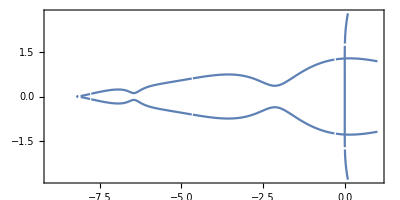

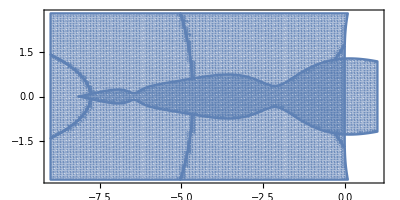

```mathematica
ClearAll["Global`*"]   (*2-step 2-stage 5-order ThDTSRK25  A-stable *)
Remove["Global`*"]
ClearAll["x*"]
ClearAll["y*"]
ClearAll["z*"]
ClearAll["f*"]
θ=0;
 a21=0.198389107020261;w1= 0.501187671012343;
w2=0.167743974813318;vv2=0.657963316199564;
ww2=1.49119408435601;vvv2=0.119984650586874;www2=0.0621952996182998;
(*0.198389107020261 0.501187671012343 0.167743974813318 0.657963316199564 1.49119408435601 0.119984650586874 0.0621952996182998-8.18029263691088*)
z=x+I*y;
f1[z_]:=1/120 (60+60 z-60 w1 z-60 w2 z+9 z^2+180 a21^2 vv2 z^2+120 a21^3 vv2 z^2+360 a21 vvv2 z^2+360 a21^2 vvv2 z^2+30 w1 z^2+30 w2 z^2-120 a21^3 w2 z^2-180 a21^2 ww2 z^2+120 a21^3 ww2 z^2-360 a21 www2 z^2+360 a21^2 www2 z^2+23 z^3-120 a21^2 vv2 z^3-60 a21^3 vv2 z^3-240 a21 vvv2 z^3-180 a21^2 vvv2 z^3-5 w1 z^3-5 w2 z^3+60 a21^3 w2 z^3+60 a21^2 ww2 z^3-60 a21^3 ww2 z^3+120 a21 www2 z^3-180 a21^2 www2 z^3+30 a21^2 vv2 z^4+60 a21 vvv2 z^4-10 a21^3 w2 z^4+10 a21^3 vv2 z^5+30 a21^2 vvv2 z^5+10 a21^3 vvv2 z^6-√((60-60 (-1+w1+w2) z+3 (3+10 w1+10 w2+40 a21^3 (vv2-w2+ww2)+120 a21 (vvv2-www2)+60 a21^2 (vv2+2 vvv2-ww2+2 www2)) z^2-(-23+5 w1+5 w2+60 a21^3 (vv2-w2+ww2)+120 a21 (2 vvv2-www2)+60 a21^2 (2 vv2+3 vvv2-ww2+3 www2)) z^3-10 a21 (-3 a21 vv2-6 vvv2+a21^2 w2) z^4+10 a21^2 (a21 vv2+3 vvv2) z^5+10 a21^3 vvv2 z^6)^2+240 z (5 w1 (12+6 z+z^2)+5 w2 (1+2 a21^3 z) (12+6 z+z^2)+z (21+8 z-30 a21^2 (-6 ww2+12 www2-4 ww2 z+6 www2 z-ww2 z^2-www2 z^3+6 vvv2 (2+z)+2 vv2 (3+z))-60 a21 (2 vvv2 (3+z)-www2 (6+4 z+z^2))-10 a21^3 (-www2 z^4+6 vv2 (2+z)+ww2 (12+6 z-z^3))))));
ss1=ContourPlot[Abs[f1[z]]==1,{x,-9,1},{y,-2.8,2.8},AspectRatio->1.2,PlotPoints->50] ;
rr1=RegionPlot[Abs[f1[z]]<=1,{x,-9,1.},{y,-2.8,2.8},AspectRatio->1.2,PlotPoints->100]  ;
f2[z_]:= 1/120 (60+60 z-60 w1 z-60 w2 z+9 z^2+180 a21^2 vv2 z^2+120 a21^3 vv2 z^2+360 a21 vvv2 z^2+360 a21^2 vvv2 z^2+30 w1 z^2+30 w2 z^2-120 a21^3 w2 z^2-180 a21^2 ww2 z^2+120 a21^3 ww2 z^2-360 a21 www2 z^2+360 a21^2 www2 z^2+23 z^3-120 a21^2 vv2 z^3-60 a21^3 vv2 z^3-240 a21 vvv2 z^3-180 a21^2 vvv2 z^3-5 w1 z^3-5 w2 z^3+60 a21^3 w2 z^3+60 a21^2 ww2 z^3-60 a21^3 ww2 z^3+120 a21 www2 z^3-180 a21^2 www2 z^3+30 a21^2 vv2 z^4+60 a21 vvv2 z^4-10 a21^3 w2 z^4+10 a21^3 vv2 z^5+30 a21^2 vvv2 z^5+10 a21^3 vvv2 z^6+√((60-60 (-1+w1+w2) z+3 (3+10 w1+10 w2+40 a21^3 (vv2-w2+ww2)+120 a21 (vvv2-www2)+60 a21^2 (vv2+2 vvv2-ww2+2 www2)) z^2-(-23+5 w1+5 w2+60 a21^3 (vv2-w2+ww2)+120 a21 (2 vvv2-www2)+60 a21^2 (2 vv2+3 vvv2-ww2+3 www2)) z^3-10 a21 (-3 a21 vv2-6 vvv2+a21^2 w2) z^4+10 a21^2 (a21 vv2+3 vvv2) z^5+10 a21^3 vvv2 z^6)^2+240 z (5 w1 (12+6 z+z^2)+5 w2 (1+2 a21^3 z) (12+6 z+z^2)+z (21+8 z-30 a21^2 (-6 ww2+12 www2-4 ww2 z+6 www2 z-ww2 z^2-www2 z^3+6 vvv2 (2+z)+2 vv2 (3+z))-60 a21 (2 vvv2 (3+z)-www2 (6+4 z+z^2))-10 a21^3 (-www2 z^4+6 vv2 (2+z)+ww2 (12+6 z-z^3))))));
ss2=ContourPlot[Abs[f2[z]]==1,{x,-9,1},{y,-2.8,2.8},AspectRatio->1.2,PlotPoints->50] ;
rr2=RegionPlot[Abs[f2[z]]<=1,{x,-9,1.},{y,-2.8,2.8},AspectRatio->1.2,PlotPoints->100]  ;
Show[ss1,ss2,AspectRatio->0.5]
Show[rr1,rr2,AspectRatio->0.5]
```